### Wprowadzenie wartości dla ładunku protonu ( "e" ), liczby atomowej wodoru i deuteru ( "Z" ), częstotliwości ( "f" ) i częstotliwości kołowej ( "ω" ) oraz połowy odległości między elektrodami ( "r_o" ).

```mathematica
ClearAll["Global`*"];
```

```mathematica
e=1.6×10^-19;     (* C *)
```

```mathematica
Z=1;                         (* 1 *)
```

```mathematica
f=2.7648×10^6;             (* 1/s *)
```

```mathematica
ω=2×π×f ;    (* rad/s *)
```

```mathematica
ro=0.11×25.4×10^-3                  (* m *)
```

0.002794

### Zdefiniowanie procedury "traj[U_, V_, Vz, mu_]".

```mathematica
traj[U_,V_,vz_,mu_]:=(
(* Wprowadzenie wzoru na potencjal ("ϕ") w miejscu wyznaczonym przez współrzędne "x" i "y" .  Symbole "U" i "V" oznaczają odpowiednio napięcie stałe i zmienne przyłożone  do elektrod. *)
ϕo=U+V×Cos[ω×t];
ϕ=ϕo/ro^2×(x^2-y^2);
(* Wprowadzenie wektora predkości początkowej ("v_p")  oraz wektora położenia początkowego ("r_p"). *)
vp={10.0,10.0,vz};
rp={0.0,0.0,0.0};
(* Wprowadzenie wzoru na zależność współrzędnej "z" od czasu "z[t]". *)
z[t_]=rp[[3]]+vz×t;
(* Obliczenie natężenia pola elektrycznego ("E_e") o potencjale "ϕ ". *)
Ee=-Grad[ϕ ,{x,y,z}];
(* Obliczenie wektora sily "F" działającej na jony w polu o natężeniu "E_e". *)
F=Z×e×Ee/.{x->x[t],y->y[t]};
(* Wprowadzenie wartości dla masy jonu "m". Symbol "m_u" oznacza masę atomową jonu. *)
m=1.67×mu×10^-27;
(* Numeryczne rozwiązanie   układu równań różniczkowych opisujących ruch jonów (znalezienie funkcji "x[t]" i  "y[t]"). *)
rownxy=NDSolve[{m×D[x[t], t,t]==F[[1]]×UnitStep[ro^2-(x[t]^2+y[t]^2)],D[x[t], t]==vp[[1]]/.t->0,x[0]==rp[[1]],m×D[y[t], t,t]==F[[2]]×UnitStep[ro^2-(x[t]^2+y[t]^2)],D[y[t], t]==vp[[2]]/.t->0,y[0]==rp[[2]]},{x[t],y[t]},{t,0,10^-5},MaxSteps->10^5];
(* Sporządzenie wykresu obrazującego zależność współrzędnej "x" od czasu "t". *)
Print[Plot[Evaluate[{100×x[t]}/.rownxy],{t,0,10^-5},PlotStyle->{Black,Thickness[0.006]},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotLabel->StyleForm[StringForm[" m/Z =    ``  ",mu],
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->10],
AxesLabel->{"t, s","x[t], cm"},PlotRange->{{0,8×10^-6},{-100×ro,100×ro}}]];
(* Sporządzenie wykresu obrazującego zależnosść współrzędnej "y" od czasu "t". *)
Print[Plot[Evaluate[{100×y[t]}/.rownxy],{t,0,10^-5},PlotStyle->{Black,Thickness[0.006]},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotLabel->StyleForm[StringForm[" m/Z =   ``   ",mu],
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->10],
AxesLabel->{"t, s","y[t], cm"},PlotRange->{{0,8×10^-6},{-100×ro,100×ro}}]];
(* Sporządzenie trójwymiarowego wykresu trajektorii jonu.  *)
Print[ParametricPlot3D[Evaluate[{1000×x[t],1000×y[t],100×z[t]}/.rownxy],{t,0,10^-5},PlotRange->{{-1000×ro,1000×ro},{-1000×ro,1000×ro},{0,5000×ro}},PlotStyle->{Black,Thickness[0.006]},

BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},AxesLabel->{"x, mm","y, mm                         ","z, cm"}]])
```

### Wywołanie procedury dla U = 34.5 [V], V =74.0 [V], v_z=19000 [m/s], m_u= 4 [1].

```mathematica
(*Do[traj[34.5,74.0,19000,mu],{mu,1,50,1}]*)
```

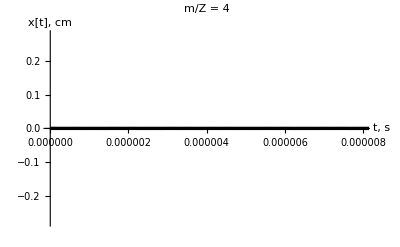

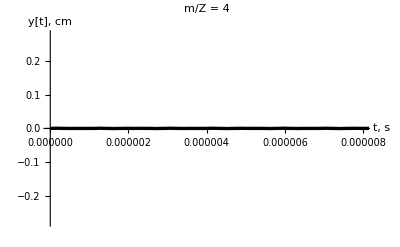

-Graphics3D-

```mathematica
traj[34.5,74.0,19000,4]
```

### Wywołanie procedury dla U = 34.5 [V], V =74.0 [V], v_z=19000 [m/s], m_u= 5 [1].

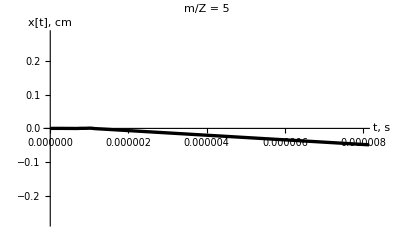

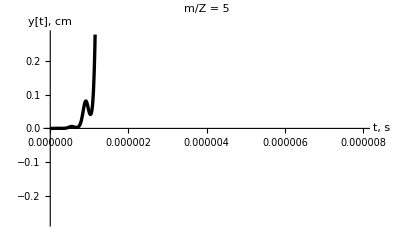

-Graphics3D-

```mathematica
traj[34.5,74.0,19000,5]
```

### Wywołanie procedury dla U = 34.5 [V], V =74.0 [V], v_z=19000 [m/s], m_u= 3 [1].

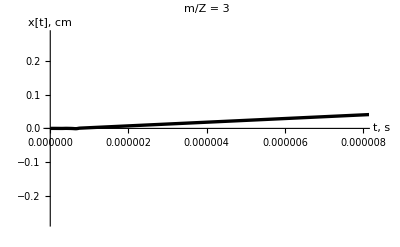

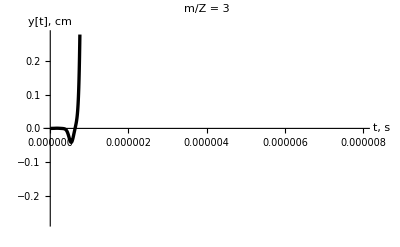

-Graphics3D-

```mathematica
traj[34.5,74.0,19000,3]
```

### Wywołanie procedury dla U = 110.5 [V], V =230 [V], v_z=11000 [m/s], m_u= 12 [1].

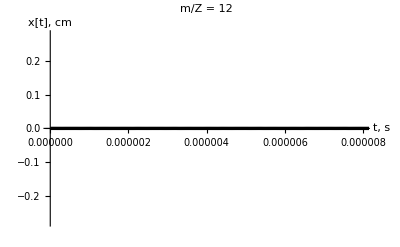

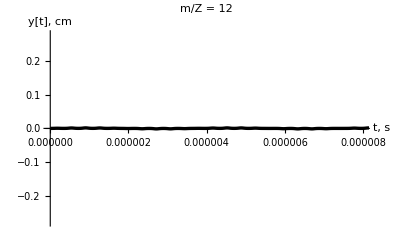

-Graphics3D-

```mathematica
traj[110.5,230,11000,12]
```

### Wywołanie procedury dla U = 110.5 [V], V =230 [V], v_z=11000 [m/s], m_u= 13 [1].

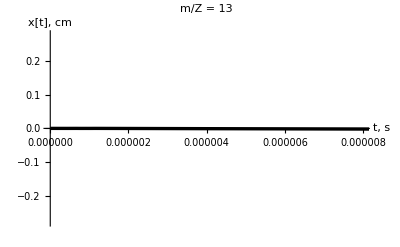

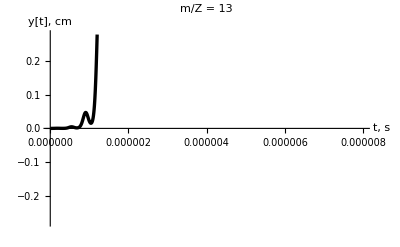

-Graphics3D-

```mathematica
traj[110.5,230,11000,13]
```

### Wywołanie procedury dla U = 110.5 [V], V =230 [V], v_z=11000 [m/s], m_u= 11 [1].

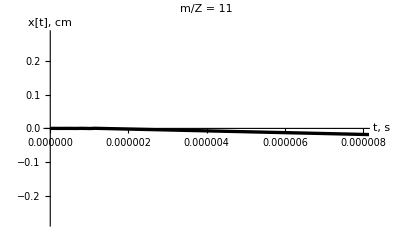

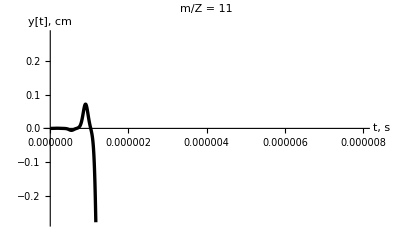

-Graphics3D-

```mathematica
traj[110.5,230,11000,11]
```